# Math 223: Homework 9

<Hardeep Bassi>

<04/11/2023>

## Problem 1

Use second-order perturbation theory to find approximations to the roots of .
Using the regular perturbation expansion , we see the equation becomes:
. Now, we compute the solution as:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],0]
```

x[0]+x[0]^2

```mathematica
Solve[x[0]+x[0]^2 == 0, x[0]]
```

{{x[0]→-1},{x[0]→0}}

For each root, we now compute the higher order solutions:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],1] /. x[0] -> 0
```

6+x[1]

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],2] /. { x[0] -> 0, x[1]-> -6 }
```

36+x[2]

Hence, we get that

Repeating the same for the other root yields:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],1] /. x[0] -> -1
```

6-x[1]

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],2] /. { x[0] -> -1, x[1]-> 6 }
```

36-x[2]

Hence, we get that

## Problem 2

Compute all of the coefficients in the perturbation series solution to the initial-value problem . Also show that the series converges for all values of . Also compute the perturbation series indirectly by expanding the explicit exact solution in powers of .

We utilize the regular perturbation expansion give by . Plugging this in for the IVP yields:
. To find the order 1 approximation, we collect terms and solve:

```mathematica
DSolve[{Subscript[y, 0]'[x]- Subscript[y, 0][x]==0,Subscript[y, 0][0]==1},Subscript[y, 0][x],x]
```

{{y_0[x]→ⅇ^x}}

We proceed with the  approximation  as follows:

```mathematica
DSolve[{Subscript[y, 1]'[x]- Subscript[y, 1][x] == x*ⅇ^x,Subscript[y, 1][0]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→(ⅇ^x x^2)/2}}

The true solution is given by:

```mathematica
DSolve[{y'[x]-y[x]-ϵ*x*y[x]==0, y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x+(x^2 ϵ)/2)}}

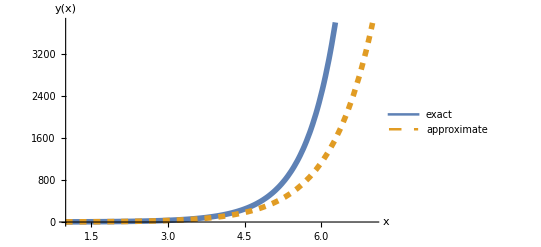

```mathematica
Plot[{ⅇ^(x+(x^2 ϵ)/2) /.ϵ->0.1,ⅇ^x+ ϵ*(ⅇ^x x^2)/2/.ϵ->0.1},{x,1,7},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

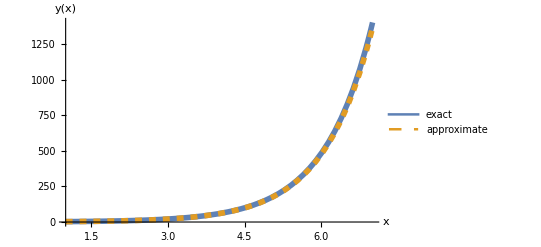

```mathematica
Plot[{ⅇ^(x+(x^2 ϵ)/2) /.ϵ->0.01,ⅇ^x+ ϵ*(ⅇ^x x^2)/2/.ϵ->0.01},{x,1,7},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

Hence, we see as we refine , we approach the true solution. Computing the next order term shows:

```mathematica
DSolve[{Subscript[y, 2]'[x]- Subscript[y, 2][x] == x*(ⅇ^x x^2)/2,Subscript[y, 2][0]==0},Subscript[y, 2][x],x]
```

{{y_2[x]→(ⅇ^x x^4)/8}}

Thus, we see that our series will be of form . By inspection, this series passes the ratio test, given that .  Finally, we expand this as:

```mathematica
Series[ⅇ^(x+(x^2 ϵ)/2), {ϵ,0,4}]
```

ⅇ^x+1/2 ⅇ^x x^2 ϵ+1/8 ⅇ^x x^4 ϵ^2+1/48 ⅇ^x x^6 ϵ^3+1/384 ⅇ^x x^8 ϵ^4+O[ϵ]^5

We see that this matches the terms that we computed, hence validates our approximation.

## Problem 3

Show that the solution to the IVP , remains bounded for all real . Obtain a first-order perturbative approximation to  and show that it is unbounded as . Conclude that the first order approximation is valid only for .

We proceed the same as the previous problem:

```mathematica
DSolve[{Subscript[y, 0]''[x]+ Subscript[y, 0][x]==0,Subscript[y, 0][0]==1, Subscript[y, 0]'[0]==0},Subscript[y, 0][x],x]
```

{{y_0[x]→Cos[x]}}

```mathematica
DSolve[{Subscript[y, 1]''[x]+ Subscript[y, 1][x] == -Cos[x],Subscript[y, 1][0]==0, Subscript[y, 1]'[0]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→1/4 (2 Cos[x]-2 Cos[x]^3-2 x Sin[x]-Sin[x] Sin[2 x])}}

The true solution is given by:

```mathematica
DSolve[{y''[x]+y[x]+ϵ*y[x]==0, y[0]==1, y'[0]==0},y[x],x]
```

{{y[x]→1/2 ⅇ^(-x √(-1-ϵ)) (1+ⅇ^(2 x √(-1-ϵ)))}}

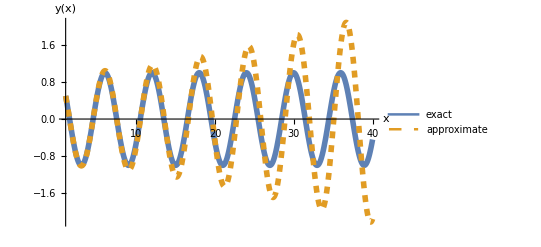

```mathematica
Plot[{1/2 ⅇ^(-x √(-1-ϵ)) (1+ⅇ^(2 x √(-1-ϵ))) /.ϵ->0.1,Cos[x] + ϵ *  1/4 (2 Cos[x]-2 Cos[x]^3-2 x Sin[x]-Sin[x] Sin[2 x])/.ϵ->0.1},{x,1,40},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

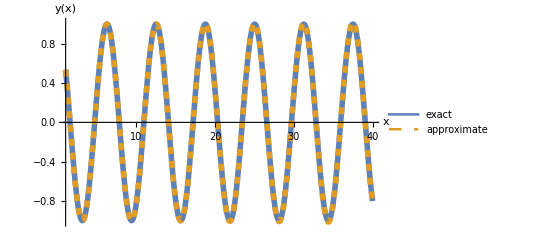

```mathematica
Plot[{1/2 ⅇ^(-x √(-1-ϵ)) (1+ⅇ^(2 x √(-1-ϵ))) /.ϵ->0.01,Cos[x] + ϵ *  1/4 (2 Cos[x]-2 Cos[x]^3-2 x Sin[x]-Sin[x] Sin[2 x])/.ϵ->0.01},{x,1,40},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

To demonstrate the unboundedness of the first order approximation, we see that as we take :

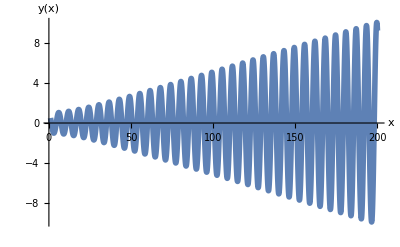

```mathematica
Plot[Cos[x] + ϵ *  1/4 (2 Cos[x]-2 Cos[x]^3-2 x Sin[x]-Sin[x] Sin[2 x])/.ϵ->0.1,{x,1,200},PlotStyle->{Directive[Solid,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

Observing the magnitude of our solution and using the triangle inequality alongside the fact that both cosine and sine are bounded shows:

Here, we see that there is an  term, hence for boundedness